## SimulationによるOLS推定の検討

### 関数のリスト

```mathematica
(*　攪乱項（誤差項）を含む真の関数からの出力　*)
er[s_]:=RandomReal[NormalDistribution[0,s]];(* 攪乱項の定義．平均は0 *)
truef1[x1_,x2_,x3_]:=20+5 x1+10 x2-15 x3+er[1];
truef2[x1_,x2_,x3_]:=20+10 x1*x2*x3+er[1];
truef3[x1_,x2_,x3_]:=20+5 x1^2+10 x2^3+Log[x3]+er[1];
truef4[x1_,x2_,x3_]:=20+Sqrt[5 x1]*Sqrt[x2]*Log[x3]+er[1];
truef5[x1_,x2_]:=Sqrt[5 x1]*x2^5+er[1];
truel6[x1_,x2_,x3_]:=20+10 x1*x2*x3+er[1];truef7[x1_,x2_]:=5*x1^3+5*x2^3+er[1];
```

### 分析

```mathematica
(* 真の関数が　線形関数　truef7　の場合  *)
Module[{population,data,lm},
population=Table[{x1,x2,truef7[x1,x2]},{x1,-5,5},{x2,-5,5}];
(* 真の関数に基づきデータを発生させる *)
population=Flatten[population,1];(*説明変数により異なる、注意*)
population=RandomSample[population];
data=population[[1;;100]](* 無作為抽出 *);
lm=LinearModelFit[data,{x1,x2},{x1,x2}];(* ここで線型回帰 *)
Normal[lm];
TableForm[
lm[{"ParameterTable","ANOVATable","AdjustedRSquared","AIC"}]
]
]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.92073 | 16.8472 | 0.114009 | 0.909466
x1 | 85.7347 | 5.44168 | 15.7552 | 1.72879×10^-28
x2 | 90.1289 | 5.43207 | 16.592 | 4.38397×10^-30
 | DF | SS | MS | F-Statistic | P-Value
x1 | 1 | 6.40402×10^6 | 6.40402×10^6 | 228.306 | 3.12425×10^-27
x2 | 1 | 7.72206×10^6 | 7.72206×10^6 | 275.295 | 4.38397×10^-30
Error | 97 | 2.72086×10^6 | 28050.2 |  | 
Total | 99 | 1.68469×10^7 |  |  | 
0.835165
1312.92

```mathematica
(* 攪乱項の定義．平均は0 *)truef5[x1_,x2_]:=5*x1^3+5*x2^3;
f1[x1_,x2_]:=-1.811+87.1738*x1+91.2*x2;
```

```mathematica
Plot3D[{truef5[x1,x2],f1[x1,x2]},{x1,-5,5},{x2,-5,5}]
```

-Graphics3D-

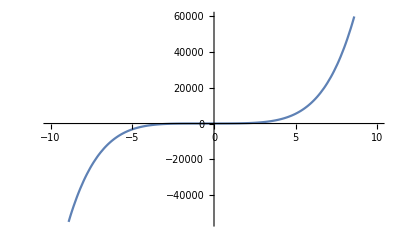

```mathematica
Plot[x^5+x^4+10*x^3+20*x^2,{x,-10,10}]
```

```mathematica
(* 真の関数が　線形関数　truef1　の場合  *)
Module[{population,data,lm},
population=Table[{x1,x2,x3,truef1[x1,x2,x3]},{x1,1,10},{x2,-1,5},{x3,1,10}];
(* 真の関数に基づきデータを発生させる *)
population=Flatten[population,2];(*説明変数により異なる、注意*)
population=RandomSample[population];
data=population[[1;;100]](* 無作為抽出 *);
lm=LinearModelFit[data,{x1,x2,x3},{x1,x2,x3}];(* ここで線型回帰 *)
Normal[lm];
TableForm[
lm[{"ParameterTable","ANOVATable","AdjustedRSquared","AIC"}]
]
]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 19.7073 | 0.370887 | 53.1354 | 5.39364×10^-73
x1 | 4.99354 | 0.0428548 | 116.522 | 3.45146×10^-105
x2 | 10.0728 | 0.0578074 | 174.247 | 6.94468×10^-122
x3 | -14.9701 | 0.0402289 | -372.124 | 1.81302×10^-153
 | DF | SS | MS | F-Statistic | P-Value
x1 | 1 | 23598.5 | 23598.5 | 17109.8 | 5.59057×10^-110
x2 | 1 | 46730.6 | 46730.6 | 33881.6 | 3.64792×10^-124
x3 | 1 | 190991. | 190991. | 138476. | 1.81302×10^-153
Error | 96 | 132.406 | 1.37923 |  | 
Total | 99 | 261452. |  |  | 
0.999478
321.858

```mathematica
(* 真の関数が　非線形関数　truef2　の場合  *)
(*  20+5 x1+10 x2-15 x3+er[1];  *)
```

```mathematica
(* truef2[x1_,x2_,x3_]:=20+10 x1*x2*x3; の場合　　真のパラメータ*)
{D[20+10 x1*x2*x3,x1],D[20+10 x1*x2*x3,x2],D[20+10 x1*x2*x3,x3]}
```

{10 x2 x3,10 x1 x3,10 x1 x2}

```mathematica
Module[{population,data,lm},
population=Table[{x1,x2,x3,truef2[x1,x2,x3]},{x1,1,10},{x2,-1,5},{x3,1,10}];
population=Flatten[population,2];(*説明変数により異なる、注意*)
population=RandomSample[population];
data=population[[1;;100]](* 無作為抽出 *);
lm=LinearModelFit[data,{x1,x2,x3},{x1,x2,x3}];(* ここで線型回帰 *)
Normal[lm];
TableForm[
lm[{"ParameterTable","ANOVATable","AdjustedRSquared","AIC"}]
]
]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1560.69 | 170.599 | -9.14828 | 1.00558×10^-14
x1 | 111.631 | 19.7872 | 5.6416 | 1.69875×10^-7
x2 | 366.81 | 26.2183 | 13.9906 | 6.66262×10^-25
x3 | 155.831 | 18.1985 | 8.56284 | 1.8052×10^-13
 | DF | SS | MS | F-Statistic | P-Value
x1 | 1 | 1.77386×10^7 | 1.77386×10^7 | 72.2927 | 2.42856×10^-13
x2 | 1 | 4.2215×10^7 | 4.2215×10^7 | 172.045 | 3.96812×10^-23
x3 | 1 | 1.79913×10^7 | 1.79913×10^7 | 73.3223 | 1.8052×10^-13
Error | 96 | 2.35557×10^7 | 245372. |  | 
Total | 99 | 1.01501×10^8 |  |  | 
0.760673
1530.76

```mathematica
Module[{population,data,lm},
population=Table[{x1,x2,x3,truef2[x1,x2,x3]},{x1,1,10},{x2,1,10},{x3,1,10}];
population=Flatten[population,2];(*説明変数により異なる、注意*)
population=RandomSample[population];
data=population[[1;;50]](* 30人抽出 *);
lm=LinearModelFit[data,{x1,x2,x3},{x1,x2,x3}];
Normal[lm];
TableForm[
lm[{"ParameterTable","ANOVATable","SinglePredictionConfidenceIntervalTable","AdjustedRSquared","AIC"}]
]
]
```

```mathematica
Module[{population,data,lm},
population=Table[{x1,x2,x3,freal2[x1,x2,x3]},{x1,-1,9},{x2,-1,9},{x3,-1,9}];
population=Flatten[population,2];(*説明変数により異なる、注意*)
population=RandomSample[population];
data=population[[1;;50]](* 30人抽出 *);
lm=LinearModelFit[data,{x1,x2,x3},{x1,x2,x3}];
Normal[lm];
lm[{"ParameterTable","ANOVATable","SinglePredictionConfidenceIntervalTable","AdjustedRSquared","AIC"}]
]
```

### Plotして比較

```mathematica
"SinglePredictionConfidenceIntervalTable",
```

```mathematica
Module[{population,data},
population=Table[{x1,x2,freal5[x1,x2]},{x1,1,100},{x2,1,100}];
population=Flatten[population,1];(*説明変数により異なる、注意*)
population=RandomSample[population];
data=population[[1;;30]](* 30人抽出 *);
lm=LinearModelFit[data,{x1,x2},{x1,x2}];
Normal[lm];
lm[{"ParameterTable","ANOVATable","AdjustedRSquared","AIC"}]
]
```

{ | Estimate | Standard Error | t Statistic | P-Value
1 | -6.13184×10^10 | 1.09533×10^10 | -5.59819 | 6.13696×10^-6
x1 | 7.38133×10^8 | 1.58941×10^8 | 4.64406 | 0.0000792732
x2 | 1.14695×10^9 | 1.55335×10^8 | 7.38371 | 6.0793×10^-8, | DF | SS | MS | F Statistic | P-Value
x1 | 1 | 2.02832×10^22 | 2.02832×10^22 | 34.3138 | 3.07988×10^-6
x2 | 1 | 3.22268×10^22 | 3.22268×10^22 | 54.5192 | 6.0793×10^-8
Error | 27 | 1.59599×10^22 | 5.91109×10^20 |  | 
Total | 29 | 6.84699×10^22 |  |  | ,0.74964,1524.83}

```mathematica
f5est[x1_,x2_]:=7.381329974416866*^8*x1+1.1469512692918165*^9*x2-6.131844389612961*^10;
```

```mathematica
Plot3D[{freal5[x1,x2],f5est[x1,x2]},{x1,1,100},{x2,1,100}]
```

-Graphics3D-

```mathematica
er[s_]:=RandomReal[NormalDistribution[0,s]];(* 攪乱項の定義．平均は0 *)truef5[x1_,x2_]:=5*x1^3+5*x2^3;
f1[x1_,x2_]:=
```

```mathematica
Plot3D[{truef5[x1,x2]},{x1,-5,5},{x2,-5,5}]
```

-Graphics3D-

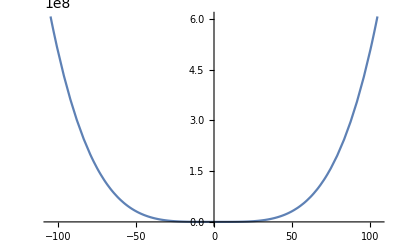

```mathematica
Plot[5*(x1)^4,{x1,-105,105}]
```

```mathematica
Plot3D[{freal5[x1,x2],f5est[x1,x2]},{x1,1,10},{x2,1,10}]
```

-Graphics3D-

### ディレクトリの設定

```mathematica
Directory[]
```

C:\Users\xps\Documents

```mathematica
"C:\\Documents and Settings\\roger\\My Documents"
```

```mathematica
(* STATAで分析する場合の*)
SetDirectory["C:\Users\sx2\Dropbox\stata"]
```

SetDirectory::cdir: 現行ディレクトリを"C:\\Users\\sx2\\Dropbox\\stata"に設定することができません．

$Failed

```mathematica
(* ver9 のディレクトリ表記は昔と違う？  *)
```

## 発展的問題

```mathematica
Q．欠落変数によってパラメータにどの程度バイアスが生じるのかを数値計算によって確かめなさい
```

```mathematica
Q．欠落変数によるバイアスを操作変数推定でどの程度除去できるか確かめなさい
```